```mathematica
SetDirectory["/home"]
```

```mathematica
f[x_]:=a0+(a2/2)*x^2+(a4/4!)*x^4
```

```mathematica
a0=33.2421;a2=0.164225;a4=49.8631;
```

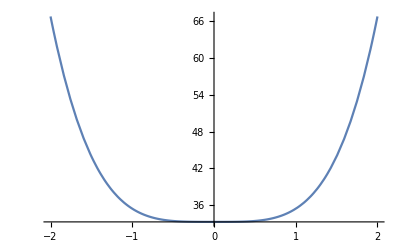

```mathematica
d=2.0;
Plot[f[x],{x,-d,d},PlotRange->All]
```

```mathematica
parts={};
```

```mathematica
Do[AppendTo[parts,{f[x],x}]
,{x,-d,d,0.0001}]
```

```mathematica
Export["1.0d_20.0alp_10.0kap_0th.dat",parts];
```